```mathematica
(* Utility functions *)
```

```mathematica
findSublistBeforeElementByValue[lst_,element_]:=lst[[ 1;;Position[lst, element][[1]][[1]]-1]]
```

```mathematica
(* Input in 1..∞ range. 1->A0, 2->A1, etc *)
```

```mathematica
vertexToName[x_,width_]:=StringJoin[FromCharacterCode[ToCharacterCode["A"][[1]]+Floor[(x-1)/width]],ToString[Mod[(x-1),width]]]
```

```mathematica
randomNumberAsString[]:=ToString[RandomInteger[{1,1000}]]
```

```mathematica
interleaveListWithRandomNumbersAsStrings[lst_]:=Riffle[lst,Table[randomNumberAsString[],Length[lst]-1]]
```

```mathematica
(* We omit division operation because micro-spreadsheet evaluator can't handle division by zero *)
```

```mathematica
interleaveListWithRandomOperationsAsStrings[lst_]:=Riffle[lst,Table[RandomChoice[{"+","-","*"}],Length[lst]-1]]
```

```mathematica
randomNonNumberExpression[g_,vertex_]:=StringJoin[interleaveListWithRandomOperationsAsStrings[interleaveListWithRandomNumbersAsStrings[Map[vertexToName[#,WIDTH]&,pickRandomNonDependentVertices[g,vertex]]]]]
```

```mathematica
pickRandomNonDependentVertices[g_,vertex_]:=DeleteDuplicates[RandomChoice[findSublistBeforeElementByValue[TopologicalSort[g],vertex],RandomInteger[{1,5}]]]
```

```mathematica
assignNumberOrExpr[g_,vertex_]:=If[VertexInDegree[g,vertex]==0,randomNumberAsString[],randomNonNumberExpression[g,vertex]]
```

```mathematica
(* Main part *) 
(* Create random graph *)
```

```mathematica
WIDTH=7;HEIGHT=8;TOTAL=WIDTH*HEIGHT
```

56

```mathematica
g=DirectedGraph[RandomGraph[BernoulliGraphDistribution[TOTAL,0.05]],"Acyclic"];
```

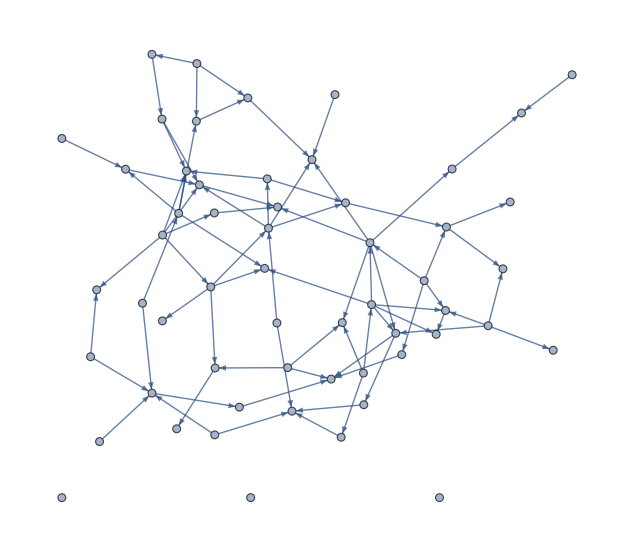

```mathematica
Graph[g]
```

```mathematica
(* Generate random expressions and numbers *)
```

```mathematica
expressions=Map[assignNumberOrExpr[g,#]&,VertexList[g]];
```

```mathematica
(* Make 2D table of it *)
```

```mathematica
t=Partition[expressions,WIDTH];
```

```mathematica
(* Export as tab-separated values *)
```

```mathematica
Export["/home/dennis/1.txt",t,"TSV"]
```

/home/dennis/1.txt

```mathematica
Grid[t,Frame->All,Alignment->Left]
```

846 | 499 | A3*913-H4 | 808 | 278 | 303 | D1+579+B6
B4*860+D2 | 999 | 59 | 442 | 425 | A5*163+B2+127*C2*927*D3*213+C1 | 583
G6*379-C3-436-C4-289+H6 | 972 | 804 | D2 | G5+108-F1*413-D3 | B5 | G4*981*D2
F2 | E0 | B6-731-D3+791+B4*92+C1 | 551 | F4*922*C2+760*A6-992+B4-184-A4 | B1-624-E3 | F4+182+A4*940-E1+76*C1
519 | G1*402+D1*107*G3-458*A1 | D3 | B4 | B3*811-D3*345+E0 | B5 | H5
F5-531+B5-222*E4 | 9 | B5+106*B6+600-B1 | E3 | A5+866*F6+695-A3*226+C6 | F4*102*E4*998-H0 | B1-616-G5+812-A5
C3-956*A5 | G4*408-D3*290*B6-899*G5+400+F1 | B2-701+H6 | A3+782*A5+46-B3-731+C1 | 42 | 287 | H0
B4-792*H4*407+F6-425-E1 | D2 | D3 | F2-327*G4*35*E1 | E1+376*A6-606*F6*554+C5 | E3 | F6*484+C1-114-H4-638-A3

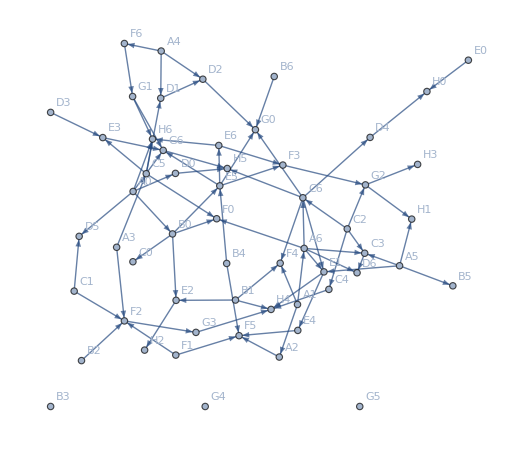

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[g,VertexLabels->Flatten[Table[{i->vertexToName[i,WIDTH]},{i,1,Length[VertexList[g]]}]]]
```